```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,18000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[0.42,0.0001,1,0]
```

1.99282

```mathematica
pris= Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[0,4,0.01]}]
```

{{0.,4.34074×10^-6},{0.01,4.35984×10^-6},{0.02,4.41789×10^-6},{0.03,4.51709×10^-6},{0.04,4.66139×10^-6},{0.05,4.85674×10^-6},{0.06,5.11169×10^-6},{0.07,5.43823×10^-6},{0.08,5.85309×10^-6},{0.09,6.37975×10^-6},{0.1,7.05164×10^-6},{0.11,7.9172×10^-6},{0.12,9.0485×10^-6},{0.13,0.0000105561},{0.14,0.0000126159},{0.15,0.000015521},{0.16,0.0000197876},{0.17,0.0000263908},{0.18,0.0000373454},{0.19,0.0000573486},{0.2,0.0000993941},{0.21,0.000210354},{0.22,0.00066514},{0.23,0.00797294},{0.24,0.991909},{0.25,0.999154},{0.26,0.99974},{0.27,0.99989},{0.28,0.999946},{0.29,0.999972},{0.3,0.999986},{0.31,0.999994},{0.32,1.},{0.33,1.},{0.34,1.00001},{0.35,1.00002},{0.36,1.00003},{0.37,1.00004},{0.38,1.00008},{0.39,1.00019},{0.4,1.00066},{0.41,1.00954},{0.42,1.99282},{0.43,1.99912},{0.44,1.9997},{0.45,1.99986},{0.46,1.99992},{0.47,1.99995},{0.48,1.99997},{0.49,1.99998},{0.5,1.99999},{0.51,1.99999},{0.52,1.99999},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.00001},{0.78,2.00001},{0.79,2.00002},{0.8,2.00003},{0.81,2.00005},{0.82,2.00011},{0.83,2.00032},{0.84,2.00226},{0.85,2.95484},{0.86,2.99854},{0.87,2.99962},{0.88,2.99984},{0.89,2.99992},{0.9,2.99996},{0.91,2.99997},{0.92,2.99998},{0.93,2.99999},{0.94,2.99999},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,2.99999},{1.61,2.99999},{1.62,2.99999},{1.63,2.99999},{1.64,2.99999},{1.65,2.99999},{1.66,2.99999},{1.67,2.99999},{1.68,2.99999},{1.69,2.99999},{1.7,2.99999},{1.71,2.99999},{1.72,3.},{1.73,3.},{1.74,2.99996},{1.75,2.99966},{1.76,2.99347},{1.77,2.00408},{1.78,2.0002},{1.79,2.00004},{1.8,2.00002},{1.81,2.00001},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,1.99999},{2.22,1.99999},{2.23,1.99999},{2.24,1.99999},{2.25,1.99999},{2.26,1.99999},{2.27,1.99999},{2.28,1.99999},{2.29,1.99999},{2.3,1.99999},{2.31,1.99999},{2.32,1.99999},{2.33,1.99999},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,1.99998},{2.39,1.9999},{2.4,1.99939},{2.41,1.98782},{2.42,1.00274},{2.43,1.00021},{2.44,1.00005},{2.45,1.00002},{2.46,1.00001},{2.47,1.00001},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,0.999999},{2.55,0.999999},{2.56,0.999999},{2.57,0.999999},{2.58,0.999998},{2.59,0.999998},{2.6,0.999997},{2.61,0.999997},{2.62,0.999997},{2.63,0.999996},{2.64,0.999996},{2.65,0.999995},{2.66,0.999995},{2.67,0.999994},{2.68,0.999994},{2.69,0.999994},{2.7,0.999993},{2.71,0.999993},{2.72,0.999993},{2.73,0.999993},{2.74,0.999994},{2.75,0.999995},{2.76,0.999996},{2.77,0.999997},{2.78,0.999999},{2.79,1.},{2.8,0.999998},{2.81,0.999984},{2.82,0.999928},{2.83,0.999657},{2.84,0.996895},{2.85,0.0243152},{2.86,0.000434578},{2.87,0.0000858531},{2.88,0.0000296068},{2.89,0.000013281},{2.9,6.96612×10^-6},{2.91,4.05834×10^-6},{2.92,2.551×10^-6},{2.93,1.69908×10^-6},{2.94,1.18465×10^-6},{2.95,8.57281×10^-7},{2.96,6.39837×10^-7},{2.97,4.9017×10^-7},{2.98,3.83999×10^-7},{2.99,3.06704×10^-7},{3.,2.49148×10^-7},{3.01,2.05435×10^-7},{3.02,1.71648×10^-7},{3.03,1.45121×10^-7},{3.04,1.24×10^-7},{3.05,1.06969×10^-7},{3.06,9.30768×10^-8},{3.07,8.16254×10^-8},{3.08,7.20952×10^-8},{3.09,6.40935×10^-8},{3.1,5.73205×10^-8},{3.11,5.15444×10^-8},{3.12,4.6584×10^-8},{3.13,4.22967×10^-8},{3.14,3.85687×10^-8},{3.15,3.5309×10^-8},{3.16,3.24437×10^-8},{3.17,2.99128×10^-8},{3.18,2.76669×10^-8},{3.19,2.56654×10^-8},{3.2,2.38745×10^-8},{3.21,2.22659×10^-8},{3.22,2.08157×10^-8},{3.23,1.95041×10^-8},{3.24,1.83139×10^-8},{3.25,1.72306×10^-8},{3.26,1.62418×10^-8},{3.27,1.53368×10^-8},{3.28,1.45063×10^-8},{3.29,1.37425×10^-8},{3.3,1.30382×10^-8},{3.31,1.23874×10^-8},{3.32,1.17847×10^-8},{3.33,1.12256×10^-8},{3.34,1.07058×10^-8},{3.35,1.02217×10^-8},{3.36,9.77014×10^-9},{3.37,9.34814×10^-9},{3.38,8.95317×10^-9},{3.39,8.58293×10^-9},{3.4,8.23537×10^-9},{3.41,7.90865×10^-9},{3.42,7.60112×10^-9},{3.43,7.31126×10^-9},{3.44,7.03774×10^-9},{3.45,6.77933×10^-9},{3.46,6.53491×10^-9},{3.47,6.30348×10^-9},{3.48,6.08411×10^-9},{3.49,5.87597×10^-9},{3.5,5.6783×10^-9},{3.51,5.49039×10^-9},{3.52,5.31159×10^-9},{3.53,5.14133×10^-9},{3.54,4.97904×10^-9},{3.55,4.82425×10^-9},{3.56,4.67648×10^-9},{3.57,4.53531×10^-9},{3.58,4.40034×10^-9},{3.59,4.27122×10^-9},{3.6,4.14761×10^-9},{3.61,4.02918×10^-9},{3.62,3.91566×10^-9},{3.63,3.80677×10^-9},{3.64,3.70226×10^-9},{3.65,3.60189×10^-9},{3.66,3.50545×10^-9},{3.67,3.41274×10^-9},{3.68,3.32355×10^-9},{3.69,3.23771×10^-9},{3.7,3.15506×10^-9},{3.71,3.07544×10^-9},{3.72,2.9987×10^-9},{3.73,2.9247×10^-9},{3.74,2.85331×10^-9},{3.75,2.78441×10^-9},{3.76,2.71788×10^-9},{3.77,2.65362×10^-9},{3.78,2.59152×10^-9},{3.79,2.53149×10^-9},{3.8,2.47344×10^-9},{3.81,2.41728×10^-9},{3.82,2.36292×10^-9},{3.83,2.3103×10^-9},{3.84,2.25934×10^-9},{3.85,2.20996×10^-9},{3.86,2.16211×10^-9},{3.87,2.11572×10^-9},{3.88,2.07074×10^-9},{3.89,2.0271×10^-9},{3.9,1.98476×10^-9},{3.91,1.94366×10^-9},{3.92,1.90376×10^-9},{3.93,1.865×10^-9},{3.94,1.82736×10^-9},{3.95,1.79077×10^-9},{3.96,1.75522×10^-9},{3.97,1.72065×10^-9},{3.98,1.68703×10^-9},{3.99,1.65433×10^-9},{4.,1.62251×10^-9}}

```mathematica
Clear[deltae,misfit2,tra,m5,ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8]
```

```mathematica
deltae[ω_,ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];tra:= Module[{},list={RandomSample[{imp,imp14,imp,imp4,imp12,imp8,imp13,imp,imp12,imp,imp2,imp11,imp,imp10,imp,imp,imp,imp10,imp13,imp5,imp2,imp,imp7,imp,imp,imp2,imp,imp,imp,imp5,imp2,imp4,imp13,imp2,imp,imp,imp,imp,imp1,imp,imp8,imp2,imp5,imp,imp11,imp,imp,imp,imp,imp,imp5,imp,imp,imp8,imp,imp,imp5,imp,imp2,imp,imp,imp,imp13,imp2,imp,imp12,imp,imp,imp,imp,imp1,imp,imp,imp,imp10,imp,imp14,imp,imp,imp13,imp,imp2,imp,imp7,imp,imp,imp,imp8,imp9,imp,imp,imp,imp,imp,imp,imp2,imp7,imp8,imp,imp}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b];
m5=tra;
ρ2:=m5- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp4.dat"][[ω*100+1]][[2]];
ρ3:= m5-Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp4.dat"][[ω*100+1]][[2]];
ρ4:=m5-Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp4.dat"][[ω*100+1]][[2]];
ρ5:=m5-Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp4.dat"][[ω*100+1]][[2]];
ρ6:= m5-Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp4.dat"][[ω*100+1]][[2]];
ρ7:= m5-Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp4.dat"][[ω*100+1]][[2]];ρ8:=m5-Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp4.dat"][[ω*100+1]][[2]];(*ρ9:=m5-Import["/home/shardulmukim/80imp100.csv"][[ω*100+1]][[2]];ρ10:=m5-Import["/home/shardulmukim/90imp100.csv"][[ω*100+1]][[2]];ρ11:=m5-Import["/home/shardulmukim/100imp100.csv"][[ω*100+1]][[2]];*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9,ρ10,ρ11*)}]
```

```mathematica
deltae[1.2,0.5,0,0]
```

{-1.31702,-0.866287,-0.556669,-0.315179,-0.137542,0.0116192,-0.0834371}

```mathematica
ρρρ=Table[deltae[1.2,0.5,0,0],1000]
```

{{-0.615282,-0.164552,0.145066,0.386556,0.564193,0.713354,0.618298},998,{-1.06835,-0.617618,-0.308,-0.0665102,0.111127,0.260288,0.165232}}
 |  |  |  |

```mathematica
aa=Table[Around[Table[Abs[ρρρ[[x]][[y]]],{x,1000}]],{y,7}]
```

{1.20.4,0.80.4,0.500.33,0.350.27,0.300.24,0.320.24,0.300.24}

```mathematica
ListPlot[aa,PlotRange->{{00,7.5},{-.10,2.1}},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1],FrameLabel->{{HoldForm[ΔΓ[n,0.5]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

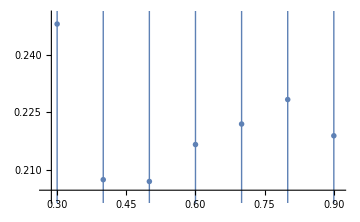

```mathematica
Table[deltae[0.42,0.5,0,0],1000]
```

{{-0.116894,-0.227278,-0.0466603,0.129937,0.207991,0.234578,0.270393,0.27707,0.284702,0.307591,1.6157},{-0.116894,-0.227278,-0.0466603,0.129937,0.207991,0.234578,0.270393,0.27707,0.284702,0.307591,0.896916},997,{-0.116894,-0.227278,-0.0466603,0.129937,0.207991,0.234578,0.270393,0.27707,0.284702,0.307591,0.71701}}
 |  |  |  |

```mathematica
Table[deltae[1,0.5,0,0],1000]
```

{{-1.70677,-1.35461,-1.06294,-0.848517,-0.662286,-0.510167,-0.365804,-0.261203,-0.181269,-0.0855589,1.8915},{-1.70677,-1.35461,-1.06294,-0.848517,-0.662286,-0.510167,-0.365804,-0.261203,-0.181269,-0.0855589,1.3392},997,{-1.70677,-1.35461,-1.06294,-0.848517,-0.662286,-0.510167,-0.365804,-0.261203,-0.181269,-0.0855589,1.64974}}
 |  |  |  |

```mathematica
Table[deltae[0.42,0.5,0,0],4000]
```

{{-0.79267,-0.903054,-0.722436,-0.545839,-0.467785,-0.441198,-0.405383,-0.398706,-0.391074,-0.368185},{-0.408541,-0.518925,-0.338307,-0.16171,-0.0836566,-0.0570696,-0.0212547,-0.014577,-0.00694568,0.0159441},3997,{-0.408639,-0.519022,-0.338405,-0.161808,-0.0837539,-0.057167,-0.0213521,-0.0146744,-0.00704305,0.0158468}}
 |  |  |  |

```mathematica
ListPlot[{Around[Table[%47[[x]][[1]],{x,1,2000}]],Around[Table[%47[[x]][[2]],{x,1,2000}]],Around[Table[%47[[x]][[3]],{x,1,2000}]],Around[Table[%47[[x]][[4]],{x,1,2000}]],Around[Table[%47[[x]][[5]],{x,1,2000}]],Around[Table[%47[[x]][[6]],{x,1,2000}]],Around[Table[%47[[x]][[7]],{x,1,2000}]],Around[Table[%47[[x]][[8]],{x,1,2000}]],Around[Table[%47[[x]][[9]],{x,1,2000}]],Around[Table[%47[[x]][[10]],{x,1,2000}]](*,Around[Table[%47[[x]][[11]],{x,1,2000}]],Around[Table[%47[[x]][[12]],{x,1,2000}]]*)}]
```

```mathematica
Table[Around[Table[Abs[%75[[x]]][[y]],{x,4000}]],{y,1,10}]
```

{0.550.34,0.630.32,0.490.35,0.40.4,0.40.4,0.40.4,0.30.4,0.30.4,0.30.4,0.30.4}

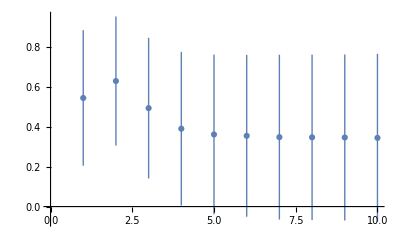

```mathematica
ListPlot[%86]
```

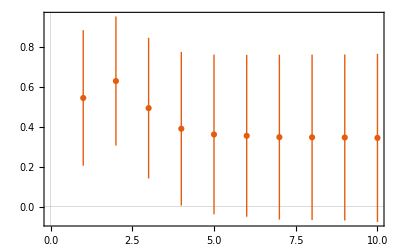

```mathematica
ListPlot[%86,PlotTheme->"Scientific"]
```

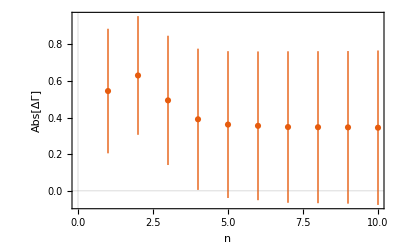

```mathematica
Show[%88,FrameLabel->{{HoldForm[Abs[ΔΓ]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
misfit2[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{},imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];lista={RandomSample[{imp2,imp,imp13,imp,imp,imp5,imp,imp,imp,imp,imp1,imp,imp,imp,imp,imp10,imp14,imp,imp,imp3,imp13,imp,imp6,imp11,imp,imp2,imp,imp12,imp,imp,imp,imp,imp,imp6,imp,imp14,imp,imp7,imp,imp3,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp9,imp10,imp9,imp,imp,imp,imp,imp1,imp,imp,imp12,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp7,imp,imp,imp,imp11,imp,imp,imp4,imp,imp,imp,imp,imp,imp}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,tra},{ω,Range[0,4,0.01]}];
υ=Module[{},
ρ1:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- pris[[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp5.csv"][[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp5.csv"][[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp5.csv"][[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp5.csv"][[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp5.csv"][[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp5.csv"][[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp5.csv"][[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];(*ρ11:=Module[{B1=Transpose[{m5[[1;;200]][[;;,1]],(m5[[1;;200,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;200,;;]][[;;,2]])}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];*)
list:={{10,100*ρ1},{1,100*ρ2},{2,100*ρ3},{3,100*ρ4},{4,100*ρ5},{5,100*ρ6},{6,100*ρ7},{7,100*ρ8},{8,100*ρ9},{9,100*ρ10}(*,{10,ρ11*)};
list];
υ]
```

```mathematica
Abs[misfit2[0.5,1.5,0]]
```

{{10,0.994766},{1,0.323796},{2,0.0105213},{3,0.185567},{4,0.316753},{5,0.412081},{6,0.477801},{7,0.53362},{8,0.593276},{9,0.619059}}

```mathematica
Table[{y,Count[Table[Position[aa[y][[x]],Min[aa[y][[x]]]][[1,1]],{x,50}],3]/50},{y,Range[0.1,2,0.1]}]
```

{{0.1,3/25},{0.2,8/25},{0.3,29/50},{0.4,7/10},{0.5,14/25},{0.6,18/25},{0.7,41/50},{0.8,43/50},{0.9,21/25},{1.,19/25},{1.1,24/25},{1.2,24/25},{1.3,1},{1.4,1},{1.5,49/50},{1.6,1},{1.7,49/50},{1.8,43/50},{1.9,23/25},{2.,24/25}}

```mathematica
Interpolation[%205]
```

InterpolatingFunction[…]

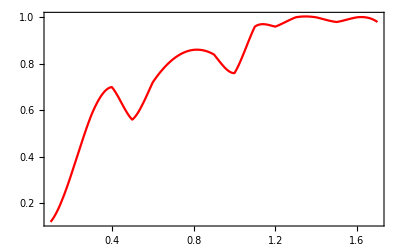

```mathematica
Plot[%207[x],{x,0.1,1.7},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotStyle->Red]
```

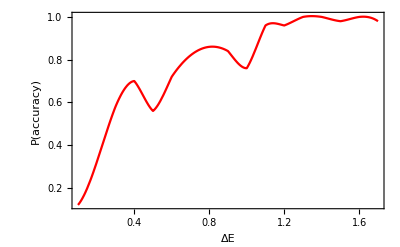

```mathematica
Show[%214,FrameLabel->{{HoldForm[P[accuracy]],None},{HoldForm[ΔΕ],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

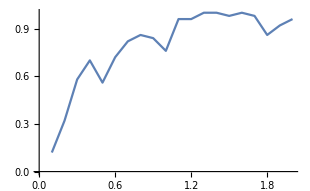

```mathematica
ListPlot[%205,Joined->True]
```

```mathematica
aa[y_]:=aa[y]=Table[Abs[misfit2[0.5,y,0]],50]
```

```mathematica
aa[0.1]
```

{{{10,1.60519×10^-6},{1,0.0000143325},{2,0.0000334073},{3,0.0000514917},{4,0.0000651853},{5,0.0000795183},{6,0.0000883034},{7,0.0000996562},{8,0.000151101},{9,0.000179132}},{{10,0.0000224692},{1,6.53147×10^-6},{2,0.0000125433},{3,0.0000306277},{4,0.0000443213},{5,0.0000586543},{6,0.0000674394},{7,0.0000787921},{8,0.000130237},{9,0.000158268}},{{10,4.76151×10^-7},{1,0.0000154616},{2,0.0000345364},{3,0.0000526207},{4,0.0000663143},{5,0.0000806474},{6,0.0000894325},{7,0.000100785},{8,0.00015223},{9,0.000180261}},{{10,7.95427×10^-6},{1,7.98346×10^-6},{2,0.0000270582},{3,0.0000451426},{4,0.0000588362},{5,0.0000731692},{6,0.0000819544},{7,0.0000933071},{8,0.000144752},{9,0.000172782}},{{10,0.0000173475},{1,1.40975×10^-6},{2,0.000017665},{3,0.0000357494},{4,0.000049443},{5,0.000063776},{6,0.0000725611},{7,0.0000839139},{8,0.000135358},{9,0.000163389}},{{10,2.80591×10^-6},{1,0.0000187436},{2,0.0000378184},{3,0.0000559028},{4,0.0000695964},{5,0.0000839294},{6,0.0000927145},{7,0.000104067},{8,0.000155512},{9,0.000183543}},{{10,0.0000223286},{1,6.39082×10^-6},{2,0.000012684},{3,0.0000307683},{4,0.0000444619},{5,0.000058795},{6,0.0000675801},{7,0.0000789328},{8,0.000130377},{9,0.000158408}},{{10,2.52324×10^-6},{1,0.000018461},{2,0.0000375357},{3,0.0000556201},{4,0.0000693137},{5,0.0000836467},{6,0.0000924319},{7,0.000103785},{8,0.000155229},{9,0.00018326}},{{10,4.93792×10^-6},{1,0.0000109998},{2,0.0000300746},{3,0.000048159},{4,0.0000618526},{5,0.0000761856},{6,0.0000849707},{7,0.0000963234},{8,0.000147768},{9,0.000175799}},{{10,0.0000462818},{1,0.0000303441},{2,0.0000112693},{3,6.81506×10^-6},{4,0.0000205086},{5,0.0000348417},{6,0.0000436268},{7,0.0000549795},{8,0.000106424},{9,0.000134455}},{{10,0.0000238607},{1,7.92299×10^-6},{2,0.0000111518},{3,0.0000292362},{4,0.0000429298},{5,0.0000572628},{6,0.0000660479},{7,0.0000774006},{8,0.000128845},{9,0.000156876}},{{10,0.0000244964},{1,8.55869×10^-6},{2,0.0000105161},{3,0.0000286005},{4,0.0000422941},{5,0.0000566271},{6,0.0000654122},{7,0.0000767649},{8,0.00012821},{9,0.00015624}},{{10,0.0000505064},{1,0.0000345686},{2,0.0000154939},{3,2.59051×10^-6},{4,0.0000162841},{5,0.0000306171},{6,0.0000394023},{7,0.000050755},{8,0.0001022},{9,0.00013023}},{{10,0.0000243491},{1,8.41138×10^-6},{2,0.0000106634},{3,0.0000287478},{4,0.0000424414},{5,0.0000567744},{6,0.0000655595},{7,0.0000769122},{8,0.000128357},{9,0.000156388}},{{10,1.80773×10^-6},{1,0.0000177455},{2,0.0000368202},{3,0.0000549046},{4,0.0000685982},{5,0.0000829312},{6,0.0000917164},{7,0.000103069},{8,0.000154514},{9,0.000182544}},{{10,0.000049378},{1,0.0000334403},{2,0.0000143655},{3,3.71888×10^-6},{4,0.0000174125},{5,0.0000317455},{6,0.0000405306},{7,0.0000518833},{8,0.000103328},{9,0.000131359}},{{10,0.0000278287},{1,0.0000118909},{2,7.18383×10^-6},{3,0.0000252682},{4,0.0000389618},{5,0.0000532948},{6,0.00006208},{7,0.0000734327},{8,0.000124877},{9,0.000152908}},{{10,0.0000332453},{1,0.0000173076},{2,1.76716×10^-6},{3,0.0000198515},{4,0.0000335451},{5,0.0000478782},{6,0.0000566633},{7,0.000068016},{8,0.000119461},{9,0.000147491}},{{10,8.09316×10^-6},{1,7.84457×10^-6},{2,0.0000269193},{3,0.0000450037},{4,0.0000586973},{5,0.0000730303},{6,0.0000818155},{7,0.0000931682},{8,0.000144613},{9,0.000172644}},{{10,0.0000225349},{1,6.5972×10^-6},{2,0.0000124776},{3,0.000030562},{4,0.0000442555},{5,0.0000585886},{6,0.0000673737},{7,0.0000787264},{8,0.000130171},{9,0.000158202}},{{10,0.0000149542},{1,9.83544×10^-7},{2,0.0000200583},{3,0.0000381427},{4,0.0000518363},{5,0.0000661693},{6,0.0000749544},{7,0.0000863072},{8,0.000137752},{9,0.000165783}},{{10,0.000105237},{1,0.0000892994},{2,0.0000702246},{3,0.0000521402},{4,0.0000384466},{5,0.0000241136},{6,0.0000153285},{7,3.97578×10^-6},{8,0.0000474688},{9,0.0000754996}},{{10,0.0000285034},{1,0.0000125657},{2,6.5091×10^-6},{3,0.0000245935},{4,0.0000382871},{5,0.0000526201},{6,0.0000614052},{7,0.0000727579},{8,0.000124203},{9,0.000152233}},{{10,1.44113×10^-6},{1,0.0000173789},{2,0.0000364536},{3,0.000054538},{4,0.0000682316},{5,0.0000825646},{6,0.0000913498},{7,0.000102702},{8,0.000154147},{9,0.000182178}},{{10,0.0000606195},{1,0.0000446818},{2,0.000025607},{3,7.52266×10^-6},{4,6.17093×10^-6},{5,0.000020504},{6,0.0000292891},{7,0.0000406418},{8,0.0000920864},{9,0.000120117}},{{10,5.89602×10^-6},{1,0.0000100417},{2,0.0000291165},{3,0.0000472009},{4,0.0000608945},{5,0.0000752275},{6,0.0000840126},{7,0.0000953653},{8,0.00014681},{9,0.000174841}},{{10,0.0000454489},{1,0.0000295111},{2,0.0000104364},{3,7.64801×10^-6},{4,0.0000213416},{5,0.0000356746},{6,0.0000444598},{7,0.0000558125},{8,0.000107257},{9,0.000135288}},{{10,0.0000906169},{1,0.0000746792},{2,0.0000556044},{3,0.00003752},{4,0.0000238264},{5,9.49339×10^-6},{6,7.08274×10^-7},{7,0.0000106444},{8,0.000062089},{9,0.0000901198}},{{10,8.55964×10^-6},{1,7.37809×10^-6},{2,0.0000264529},{3,0.0000445372},{4,0.0000582308},{5,0.0000725639},{6,0.000081349},{7,0.0000927017},{8,0.000144146},{9,0.000172177}},{{10,1.90585×10^-6},{1,0.0000140319},{2,0.0000331067},{3,0.000051191},{4,0.0000648846},{5,0.0000792177},{6,0.0000880028},{7,0.0000993555},{8,0.0001508},{9,0.000178831}},{{10,2.80682×10^-6},{1,0.0000131309},{2,0.0000322057},{3,0.0000502901},{4,0.0000639837},{5,0.0000783167},{6,0.0000871018},{7,0.0000984545},{8,0.000149899},{9,0.00017793}},{{10,0.0000239531},{1,8.01533×10^-6},{2,0.0000110594},{3,0.0000291438},{4,0.0000428374},{5,0.0000571704},{6,0.0000659556},{7,0.0000773083},{8,0.000128753},{9,0.000156784}},{{10,5.27953×10^-6},{1,0.0000106582},{2,0.000029733},{3,0.0000478174},{4,0.0000615109},{5,0.000075844},{6,0.0000846291},{7,0.0000959818},{8,0.000147426},{9,0.000175457}},{{10,0.000048466},{1,0.0000325282},{2,0.0000134535},{3,4.63091×10^-6},{4,0.0000183245},{5,0.0000326575},{6,0.0000414427},{7,0.0000527954},{8,0.00010424},{9,0.000132271}},{{10,0.0000366256},{1,0.0000206879},{2,1.61313×10^-6},{3,0.0000164712},{4,0.0000301648},{5,0.0000444979},{6,0.000053283},{7,0.0000646357},{8,0.00011608},{9,0.000144111}},{{10,0.000112323},{1,0.0000963849},{2,0.0000773101},{3,0.0000592257},{4,0.0000455321},{5,0.0000311991},{6,0.000022414},{7,0.0000110613},{8,0.0000403833},{9,0.0000684141}},{{10,0.0000364993},{1,0.0000205616},{2,1.4868×10^-6},{3,0.0000165976},{4,0.0000302912},{5,0.0000446242},{6,0.0000534093},{7,0.000064762},{8,0.000116207},{9,0.000144237}},{{10,0.0000616302},{1,0.0000456925},{2,0.0000266177},{3,8.53335×10^-6},{4,5.16024×10^-6},{5,0.0000194933},{6,0.0000282784},{7,0.0000396311},{8,0.0000910757},{9,0.000119106}},{{10,0.0000824438},{1,0.0000665061},{2,0.0000474313},{3,0.0000293469},{4,0.0000156534},{5,1.32032×10^-6},{6,7.4648×10^-6},{7,0.0000188175},{8,0.0000702621},{9,0.0000982929}},{{10,0.000023053},{1,7.11531×10^-6},{2,0.0000119595},{3,0.0000300438},{4,0.0000437374},{5,0.0000580705},{6,0.0000668556},{7,0.0000782083},{8,0.000129653},{9,0.000157684}},{{10,0.0000970317},{1,0.000081094},{2,0.0000620192},{3,0.0000439348},{4,0.0000302413},{5,0.0000159082},{6,7.1231×10^-6},{7,4.22961×10^-6},{8,0.0000556742},{9,0.000083705}},{{10,0.0000162412},{1,3.03446×10^-7},{2,0.0000187713},{3,0.0000368557},{4,0.0000505493},{5,0.0000648823},{6,0.0000736675},{7,0.0000850202},{8,0.000136465},{9,0.000164496}},{{10,0.0000556253},{1,0.0000396876},{2,0.0000206128},{3,2.52842×10^-6},{4,0.0000111652},{5,0.0000254982},{6,0.0000342833},{7,0.000045636},{8,0.0000970806},{9,0.000125111}},{{10,0.0000110257},{1,4.91205×10^-6},{2,0.0000239868},{3,0.0000420712},{4,0.0000557648},{5,0.0000700978},{6,0.000078883},{7,0.0000902357},{8,0.00014168},{9,0.000169711}},{{10,0.0000142479},{1,1.68981×10^-6},{2,0.0000207646},{3,0.000038849},{4,0.0000525426},{5,0.0000668756},{6,0.0000756607},{7,0.0000870134},{8,0.000138458},{9,0.000166489}},{{10,0.0000143233},{1,1.61447×10^-6},{2,0.0000206892},{3,0.0000387736},{4,0.0000524672},{5,0.0000668002},{6,0.0000755854},{7,0.0000869381},{8,0.000138383},{9,0.000166413}},{{10,0.0000312201},{1,0.0000152823},{2,3.79246×10^-6},{3,0.0000218768},{4,0.0000355704},{5,0.0000499035},{6,0.0000586886},{7,0.0000700413},{8,0.000121486},{9,0.000149517}},{{10,4.34546×10^-6},{1,0.0000115923},{2,0.000030667},{3,0.0000487514},{4,0.000062445},{5,0.000076778},{6,0.0000855632},{7,0.0000969159},{8,0.00014836},{9,0.000176391}},{{10,0.000136208},{1,0.00012027},{2,0.000101195},{3,0.000083111},{4,0.0000694175},{5,0.0000550844},{6,0.0000462993},{7,0.0000349466},{8,0.000016498},{9,0.0000445288}},{{10,0.0000594567},{1,0.000043519},{2,0.0000244442},{3,6.3598×10^-6},{4,7.33379×10^-6},{5,0.0000216668},{6,0.0000304519},{7,0.0000418047},{8,0.0000932493},{9,0.00012128}}}

```mathematica
Clear[aa]
```

```mathematica
bb=Table[{y-1,100*Abs[Around[Table[Abs[aa[[x]][[y]]], {x, 50}]]]},{y,10}]
```

{{0,0.970.05},{1,0.300.05},{2,0.0410.033},{3,0.210.05},{4,0.340.05},{5,0.440.05},{6,0.500.05},{7,0.560.05},{8,0.620.05},{9,0.640.05}}

```mathematica
Show[ListPlot[bb,FrameTicks->{{Automatic,None},{Automatic,None}},Frame->True,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1],PlotRange->All,FrameLabel->{{HoldForm[χ[n,0.5]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}],ListLinePlot[{Table[{2,y},{y,Range[0,1,0.005]}],Table[{2,y},{y,Range[0.0,1,0.0005]}]},PlotStyle->{{Dashing[{0.01,0.02,2*^-2,1*^-2}],Red},{Dashing[{0.01,0.02,2*^-2,1*^-2}],Red}},PlotRange->{{0,7},{0,7}}]]
```

-Graphics-

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],(*RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],*)Table[imp,72]]]
```

{imp2,imp,imp13,imp,imp,imp5,imp,imp,imp,imp,imp1,imp,imp,imp,imp,imp10,imp14,imp,imp,imp3,imp13,imp,imp6,imp11,imp,imp2,imp,imp12,imp,imp,imp,imp,imp,imp6,imp,imp14,imp,imp7,imp,imp3,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp9,imp10,imp9,imp,imp,imp,imp,imp1,imp,imp,imp12,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp7,imp,imp,imp,imp11,imp,imp,imp4,imp,imp,imp,imp,imp,imp}

```mathematica
Tally[{imp2,imp,imp13,imp,imp,imp5,imp,imp,imp,imp,imp1,imp,imp,imp,imp,imp10,imp14,imp,imp,imp3,imp13,imp,imp6,imp11,imp,imp2,imp,imp12,imp,imp,imp,imp,imp,imp6,imp,imp14,imp,imp7,imp,imp3,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp9,imp10,imp9,imp,imp,imp,imp,imp1,imp,imp,imp12,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp7,imp,imp,imp,imp11,imp,imp,imp4,imp,imp,imp,imp,imp,imp}]
```

{{imp2,2},{imp,72},{imp13,2},{imp5,2},{imp1,2},{imp10,2},{imp14,2},{imp3,2},{imp6,2},{imp11,2},{imp12,2},{imp7,2},{imp4,2},{imp8,2},{imp9,2}}